# With Radial Offsets

## streakline.c

version 11-  snapshot at 6000th timestep, without offset
NFW parameters = {417.0 * pow(10,3) * mau * secyr, 36.54 * kpcau, 90.0 * pi / 180, 1.0, 1.0, 0.94}

N = 6000, dt = 1,000,000 years, M = 1
Mass of Cluster = 20,000 Msun (no mass loss)
Initial Position of Cluster = 50 kpc,0,0
Initial Velocity of Cluster = 0.5 * centripetal velocity
Rcl = 20 pc = 4.126 * 10^6 AU

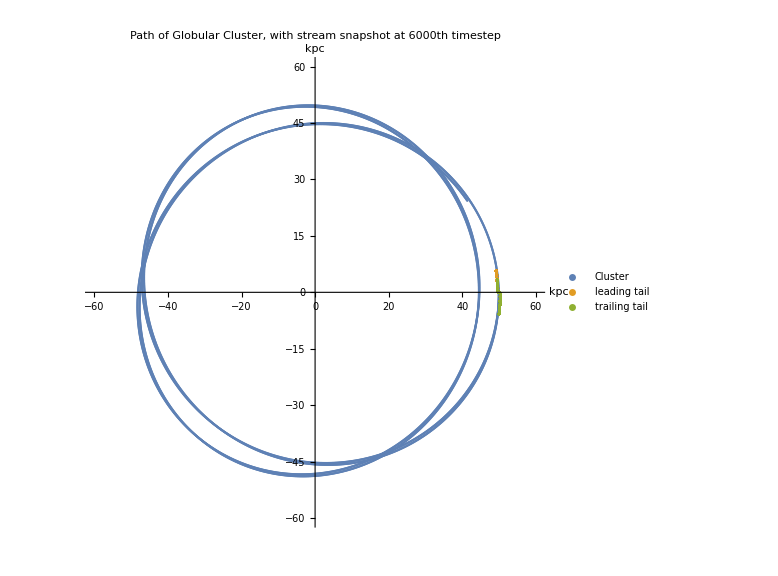

```mathematica
c11cl = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/ctest11.csv",{"Data",3;;6000,1;;2}];
c11dt =Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/ctest11.csv",{"Data",2,1;;12000}];
c11lt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/ctest11.csv",{"Data",3;;6000,4;;5}];
c11ltv = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/ctest11.csv",{"Data",3;;6000,6;;7}];
c11tt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/ctest11.csv",{"Data",3;;6000,8;;9}];
c11ttv = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/ctest11.csv",{"Data",3;;6000,10;;11}];
c11graph = ListPlot[{c11cl,c11lt,c11tt},PlotRange->{{-60,60},{-60,60}},AspectRatio->1,ImageSize->Large,PlotLegends->{"Cluster","leading tail","trailing tail"},AxesLabel->{"kpc","kpc"},PlotLabel->"Path of Globular Cluster, with stream snapshot at 6000th timestep"]
```

version 10-  initial positions of ejected stars, without offset
NFW parameters = {417.0 * pow(10,3) * mau * secyr, 36.54 * kpcau, 90.0 * pi / 180, 1.0, 1.0, 0.94}

N = 6000, dt = 1,000,000 years, M = 1
Mass of Cluster = 20,000 Msun (no mass loss)
Initial Position of Cluster = 50 kpc,0,0
Initial Velocity of Cluster = 0.5 * centripetal velocity
Rcl = 20 pc = 4.126 * 10^6 AU

```mathematica
c10cl = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/ctest10.csv",{"Data",6001,1;;2}];
c10dt =Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/ctest10.csv",{"Data",2;;6000,1;;2}];
c10lt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/ctest10.csv",{"Data",2;;6000,3;;4}];
c10ltv = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/ctest10.csv",{"Data",2;;6000,5;;6}];
c10tt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/ctest10.csv",{"Data",2;;6000,7;;8}];
c10ttv = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/ctest10.csv",{"Data",2;;6000,9;;10}];
```

Import::noelem: The Import element "6001" is not present when importing as CSV.

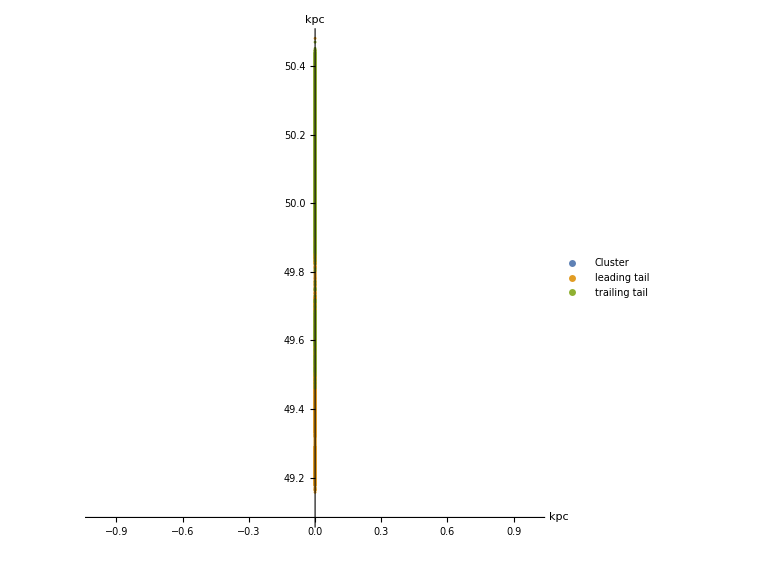

```mathematica
c10graph = ListPlot[{c10cl,c10lt,c10tt},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"Cluster","leading tail","trailing tail"},AxesLabel->{"kpc","kpc"}]
```

version 8 -  initial positions of ejected stars 
NFW parameters = {417.0 * pow(10,3) * mau * secyr, 36.54 * kpcau, 90.0 * pi / 180, 1.0, 1.0, 0.94}
offset = 0.2, 0.2
N = 6000, dt = 1,000,000 years, M = 1
Mass of Cluster = 20,000 Msun (no mass loss)
Initial Position of Cluster = 50 kpc,0,0
Initial Velocity of Cluster = 0.5 * centripetal velocity
Rcl = 20 pc = 4.126 * 10^6 AU

```mathematica
c8cl = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/ctest8.csv",{"Data",6001,1;;2}];
c8dt =Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/ctest8.csv",{"Data",2;;6000,1;;2}];
c8lt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/ctest8.csv",{"Data",2;;6000,3;;4}];
c8ltv = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/ctest8.csv",{"Data",2;;6000,5;;6}];
c8tt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/ctest8.csv",{"Data",2;;6000,7;;8}];
c8ttv = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/ctest8.csv",{"Data",2;;6000,9;;10}];
```

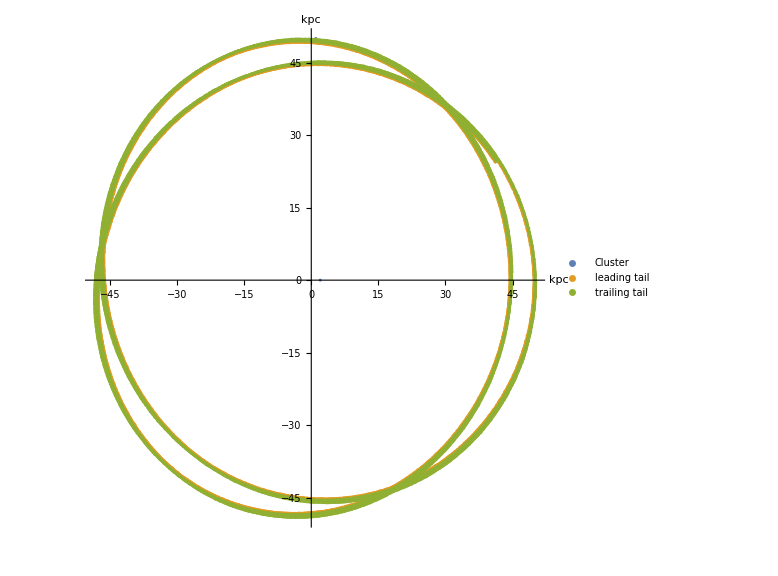

```mathematica
c8graph = ListPlot[{c8cl,c8lt,c8tt},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"Cluster","leading tail","trailing tail"},AxesLabel->{"kpc","kpc"}]
```

version 9 -  snapshot at 6000th timestep
NFW parameters = {417.0 * pow(10,3) * mau * secyr, 36.54 * kpcau, 90.0 * pi / 180, 1.0, 1.0, 0.94}
offset = 1.0,1.0
N = 6000, dt = 1,000,000 years, M = 1
Mass of Cluster = 20,000 Msun (no mass loss)
Initial Position of Cluster = 50 kpc,0,0
Initial Velocity of Cluster = 0.5 * centripetal velocity
Rcl = 20 pc = 4.126 * 10^6 AU

```mathematica
c9cl = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/ctest9.csv",{"Data",3;;6000,1;;2}];
c9dt =Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/ctest9.csv",{"Data",2,1;;12000}]
c9lt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/ctest9.csv",{"Data",3;;6000,3;;4}];
c9ltv = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/ctest9.csv",{"Data",3;;6000,5;;6}];
c9tt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/ctest9.csv",{"Data",3;;6000,7;;8}];
c9ttv = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/ctest9.csv",{"Data",3;;6000,9;;10}];
```

{0.291551,0.583809,0.364104,0.790958,0.531965,0.457705,0.141905,0.226466,0.749222,0.566114,0.4466,0.296958,0.58922,0.556575,0.310393,0.393847,0.662148,1.03076,0.803801,0.893359,0.929862,0.621534,0.709662,0.975074,0.655935,0.284806,0.511114,0.682545,0.723982,0.456566,0.558106,11938,0.513725,0.666022,0.384609,0.254745,0.454384,0.826607,0.505909,0.534,0.661606,0.639902,0.484508,0.802877,0.755308,0.162238,0.408721,0.440603,0.539318,0.629549,0.750546,0.543221,0.738839,0.608812,0.356831,1.13127,0.671212,0.966751,0.695786,1.01375,0.670732,0.703464,0.717683}
 |  |  |  |

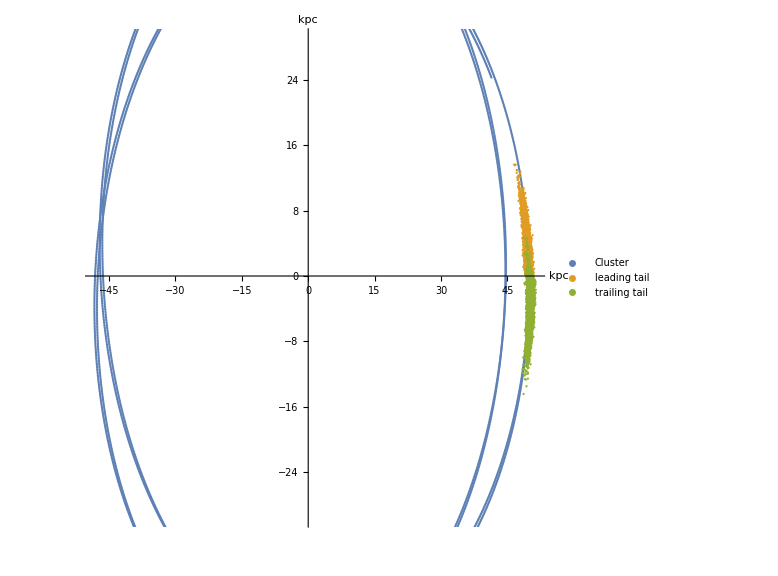

```mathematica
c9graph = ListPlot[{c9cl,c9lt,c9tt},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"Cluster","leading tail","trailing tail"},AxesLabel->{"kpc","kpc"}]
```

## streakline.chpl

version 21 - initial positions of stars at ejection (using c’s radial offsets)
NFW parameters = {417.0 * pow(10,3) * mau * secyr, 36.54 * kpcau, 90.0 * pi / 180, 1.0, 1.0, 0.94}
offset = 0.2, 0.2
N = 6000, dt = 1,000,000 years, M = 1
Mass of Cluster = 20,000 Msun (no mass loss)
Initial Position of Cluster = 50 kpc,0,0
Initial Velocity of Cluster = 0.5 * centripetal velocity
Rcl = 20 pc = 4.126 * 10^6 AU

```mathematica
ch21cl = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/test21.csv",{"Data",6001,1;;2}];
ch21dt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/test21.csv",{"Data",2;;6000,1;;2}];
ch21lt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/test21.csv",{"Data",2;;6000,3;;4}];
ch21ltv = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/test21.csv",{"Data",2;;6000,5;;6}];
ch21tt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/test21.csv",{"Data",2;;6000,7;;8}];
ch21ttv = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/test21.csv",{"Data",2;;6000,9;;10}];
```

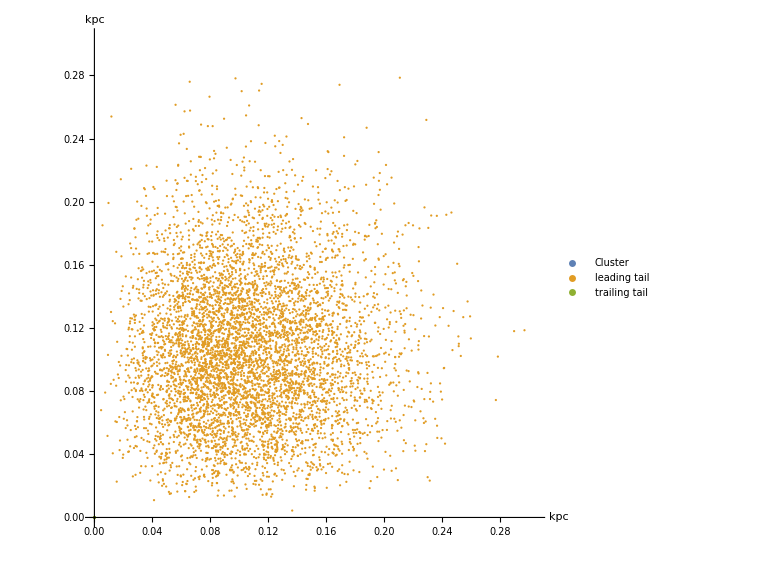

```mathematica
ch21graph = ListPlot[{ch21cl,ch21lt,ch21tt},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"Cluster","leading tail","trailing tail"},AxesLabel->{"kpc","kpc"}]
```

version 22 - initial positions of stars at ejection (using chapel’s random numbers)
NFW parameters = {417.0 * pow(10,3) * mau * secyr, 36.54 * kpcau, 90.0 * pi / 180, 1.0, 1.0, 0.94}
offset = 0.2, 0.2
N = 6000, dt = 1,000,000 years, M = 1
Mass of Cluster = 20,000 Msun (no mass loss)
Initial Position of Cluster = 50 kpc,0,0
Initial Velocity of Cluster = 0.5 * centripetal velocity
Rcl = 20 pc = 4.126 * 10^6 AU

```mathematica
ch22cl = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/test22.csv",{"Data",6001,1;;2}];
ch22dt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/test22.csv",{"Data",2;;6000,1;;2}];
ch22lt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/test22.csv",{"Data",2;;6000,3;;4}];
ch22ltv = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/test22.csv",{"Data",2;;6000,5;;6}];
ch22tt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/test22.csv",{"Data",2;;6000,7;;8}];
ch22ttv = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/test22.csv",{"Data",2;;6000,9;;10}];
```

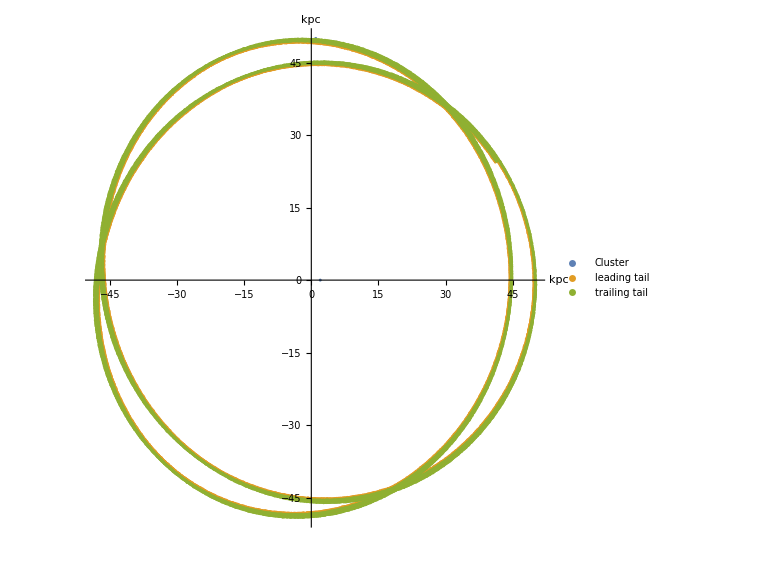

```mathematica
ch22graph = ListPlot[{ch22cl,ch22lt,ch22tt},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"Cluster","leading tail","trailing tail"},AxesLabel->{"kpc","kpc"}]
```

version 23 -snapshot at 6000th timestep
NFW parameters = {417.0 * pow(10,3) * mau * secyr, 36.54 * kpcau, 90.0 * pi / 180, 1.0, 1.0, 0.94}
offset = 1.0,1.0
N = 6000, dt = 1,000,000 years, M = 1
Mass of Cluster = 20,000 Msun (no mass loss)
Initial Position of Cluster = 50 kpc,0,0
Initial Velocity of Cluster = 0.5 * centripetal velocity
Rcl = 20 pc = 4.126 * 10^6 AU

```mathematica
ch23cl = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/test23.csv",{"Data",3;;6000,1;;2}];
ch23dt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/test23.csv",{"Data",2,1;;12000}];
ch23lt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/test23.csv",{"Data",3;;6000,5;;6}];
ch23ltv = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/test23.csv",{"Data",3;;6000,7;;8}];
ch23tt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/test23.csv",{"Data",3;;6000,9;;10}];
ch23ttv = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/test23.csv",{"Data",3;;6000,11;;12}];
```

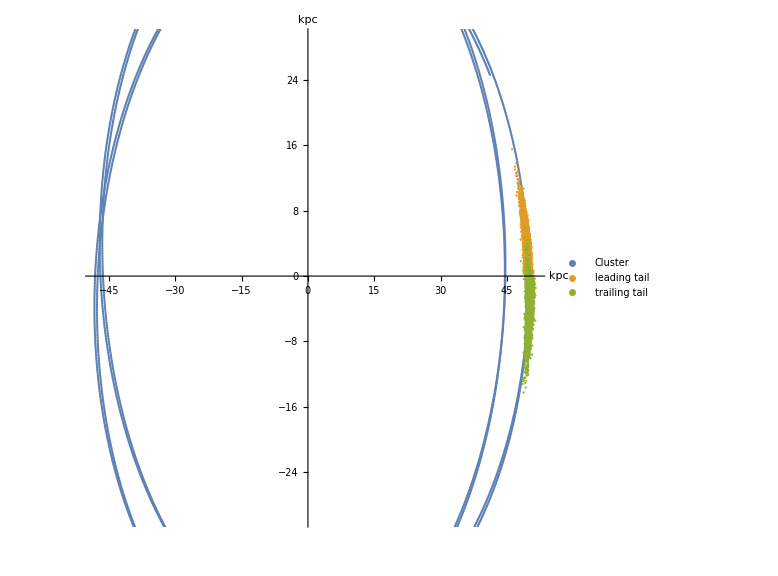

```mathematica
ch23graph = ListPlot[{ch23cl,ch23lt,ch23tt},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"Cluster","leading tail","trailing tail"},AxesLabel->{"kpc","kpc"}]
```

version 24 - initial positions of stars at ejection without random offsets
NFW parameters = {417.0 * pow(10,3) * mau * secyr, 36.54 * kpcau, 90.0 * pi / 180, 1.0, 1.0, 0.94}
offset = 0.2, 0.2
N = 6000, dt = 1,000,000 years, M = 1
Mass of Cluster = 20,000 Msun (no mass loss)
Initial Position of Cluster = 50 kpc,0,0
Initial Velocity of Cluster = 0.5 * centripetal velocity
Rcl = 20 pc = 4.126 * 10^6 AU

```mathematica
ch24cl = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/test24.csv",{"Data",6001,1;;2}];
ch24dt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/test24.csv",{"Data",2;;6000,1;;2}];
ch24lt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/test24.csv",{"Data",2;;6000,3;;4}];
ch24ltv = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/test24.csv",{"Data",2;;6000,5;;6}];
ch24tt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/test24.csv",{"Data",2;;6000,7;;8}];
ch24ttv = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/test24.csv",{"Data",2;;6000,9;;10}];
```

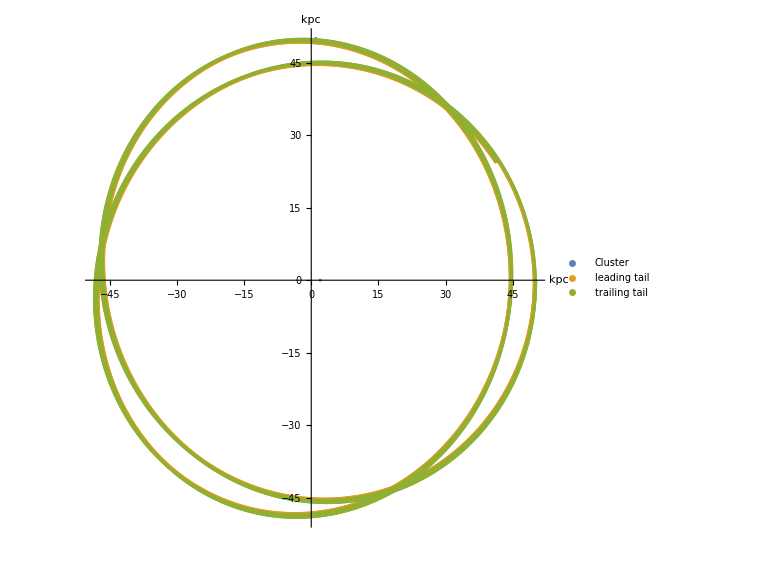

```mathematica
ch24graph = ListPlot[{ch24cl,ch24lt,ch24tt},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"Cluster","leading tail","trailing tail"},AxesLabel->{"kpc","kpc"}]
```

version 25 - 6000th timestep snapshot without radial offsets 
NFW parameters = {417.0 * pow(10,3) * mau * secyr, 36.54 * kpcau, 90.0 * pi / 180, 1.0, 1.0, 0.94}
offset = 0.2, 0.2
N = 6000, dt = 1,000,000 years, M = 1
Mass of Cluster = 20,000 Msun (no mass loss)
Initial Position of Cluster = 50 kpc,0,0
Initial Velocity of Cluster = 0.5 * centripetal velocity
Rcl = 20 pc = 4.126 * 10^6 AU

Import::someelem: One or more elements in the part specification "1;;12000" are not present when importing as CSV.

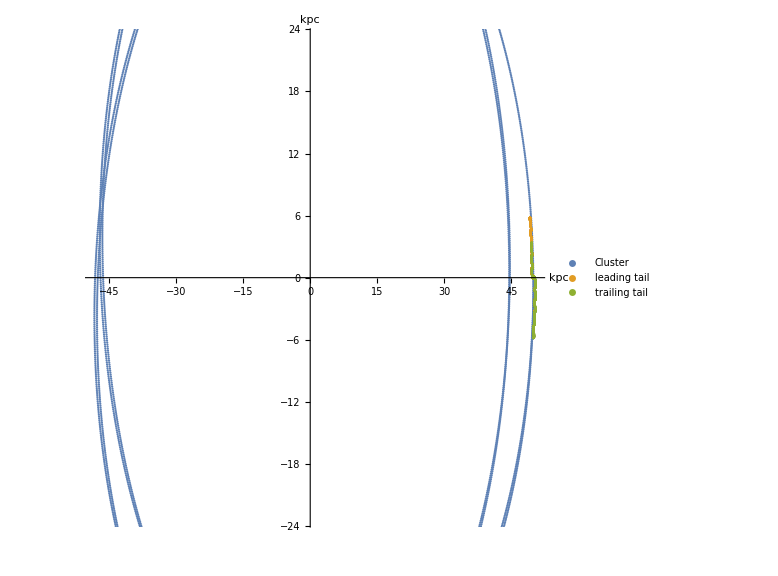

```mathematica
ch25cl = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/test25.csv",{"Data",3;;6000,1;;2}];
ch25dt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/test25.csv",{"Data",2,1;;12000}];
ch25lt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/test25.csv",{"Data",3;;6000,7;;8}];
ch25ltv = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/test25.csv",{"Data",3;;6000,9;;10}];
ch25tt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/test25.csv",{"Data",3;;6000,11;;12}];
ch25ttv = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/test25.csv",{"Data",3;;6000,13;;14}];
ch25graph = ListPlot[{ch25cl,ch25lt,ch25tt},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"Cluster","leading tail","trailing tail"},AxesLabel->{"kpc","kpc"}]
```

## Differences

c version 8 vs chapel version 21

```mathematica
diffc8ch21cl = Differences[{c8cl,ch21cl}]
diffc8ch21dt = Differences[{c8dt,ch21dt}]
diffc8ch21lt = Differences[{c8lt,ch21lt}]
diffc8ch21ltv = Differences[{c8ltv,ch21ltv}]
diffc8ch21tt = Differences[{c8tt,ch21tt}]
diffc8ch21ttv = Differences[{c8ttv,ch21ttv}]
```

{{0.0000359,-5.36078×10^-12}}

{{{1.0359×10^-8,2.68586×10^-7},{-3.37756×10^-8,4.25393×10^-7},{-8.08869×10^-8,-4.3705×10^-8},{1.50715×10^-8,-1.58604×10^-8},{-3.23554×10^-7,2.33342×10^-7},{5.0304×10^-8,-2.94689×10^-8},5987,{1.07695×10^-7,-1.12075×10^-7},{-2.40019×10^-7,1.46798×10^-7},{-4.40163×10^-7,-9.08256×10^-9},{2.76221×10^-7,-3.22086×10^-7},{-2.49624×10^-7,-1.55152×10^-7},{4.27534×10^-8,-3.65186×10^-7}}}
 |  |  |  |

{{{-41.0731,-24.284},{-40.9343,-24.4421},{-40.8146,-24.6648},{-40.8021,-24.883},{-40.5455,-24.9881},{-40.4848,-25.1492},{-40.3382,-25.1955},{-40.369,-25.4358},{-40.1092,-25.4004},{-39.9216,-25.5566},{-39.8589,-25.8412},5978,{-49.6669,1.70553},{-49.6827,1.55775},{-49.8347,1.33985},{-49.7664,1.17073},{-49.7262,1.09105},{-49.7455,0.879258},{-49.7535,0.638896},{-49.6416,0.576589},{-49.6896,0.324167},{-49.6748,0.133007}}}
 |  |  |  |

{{{41.1314,24.4007},{41.0071,24.6003},{40.921,24.7564},{40.8305,24.9283},{40.6953,25.1013},{40.5741,25.2086},{40.456,25.3069},5985,{49.8545,-1.06287},{49.8521,-0.94094},{49.8541,-0.73149},{49.8753,-0.56753},{49.8679,-0.442347},{49.883,-0.18501},{49.8775,0.0011388}}}
 |  |  |  |

{{{-41.3565,-24.534},{-41.2556,-24.7225},{-41.2019,-24.8658},{-41.0459,-25.0436},{-40.9697,-25.2493},{-40.8184,-25.4033},{-40.7531,-25.4958},5985,{-50.1338,1.11481},{-50.1416,0.938963},{-50.1875,0.785189},{-50.1732,0.590169},{-50.1628,0.346334},{-50.1779,0.14039},{-50.1558,0.0193651}}}
 |  |  |  |

{{{41.3565,24.534},{41.2556,24.7225},{41.2019,24.8658},{41.0459,25.0436},{40.9697,25.2493},{40.8184,25.4033},{40.7531,25.4958},5985,{50.1338,-1.11481},{50.1416,-0.938963},{50.1875,-0.785189},{50.1732,-0.590169},{50.1628,-0.346334},{50.1779,-0.14039},{50.1558,-0.0193651}}}
 |  |  |  |

c version 8 vs chapel version 22

```mathematica
diffc8ch22cl = Differences[{c8cl,ch22cl}]
diffc8ch22dt = Differences[{c8dt,ch22dt}]
diffc8ch22lt = Differences[{c8lt,ch22lt}]
diffc8ch22ltv = Differences[{c8ltv,ch22ltv}]
diffc8ch22tt = Differences[{c8tt,ch22tt}]
diffc8ch22ttv = Differences[{c8ttv,ch22ttv}]
```

{{0.0000359,-5.36078×10^-12}}

{{{0.0240294,-0.0697587},{0.11645,-0.00653857},{-0.0247933,-0.015832},{0.0930939,0.0365812},{-0.108198,-0.0634501},{0.0921611,0.00912957},{0.095952,0.0781269},5986,{0.118867,-0.0550458},{-0.0684877,0.0408421},{0.0304686,-0.0207862},{-0.0433627,-0.0164553},{-0.0598302,-0.0499973},{-0.126055,0.0159826}}}
 |  |  |  |

{{{0.01079,0.014769},{0.081111,-0.031719},{-0.012289,-0.008968},{0.01162,-0.075607},{-0.024711,-0.02193},{0.02093,-0.036886},{-0.033095,0.027936},5986,{-0.016769,0.037891},{-0.020995,0.056236},{-0.013898,0.00114},{-0.025475,0.085622},{-0.030471,0.011996},{-0.03133,-0.0163593}}}
 |  |  |  |

{{{-9.9809×10^-11,-5.9771×10^-11},{-4.84198×10^-10,-2.90087×10^-10},{1.02803×10^-10,6.2623×10^-11},{-3.85188×10^-10,-2.35441×10^-10},{4.46645×10^-10,2.74406×10^-10},{-3.80079×10^-10,-2.35306×10^-10},5987,{-5.76188×10^-10,1.0045×10^-11},{3.32006×10^-10,-4.499×10^-12},{-1.47708×10^-10,1.484×10^-12},{2.1022×10^-10,-1.552×10^-12},{2.90062×10^-10,-7.2×10^-13},{6.11134×10^-10,-3.04×10^-13}}}
 |  |  |  |

{{{0.0567251,0.0241137},{0.0380693,0.0480709},{-0.0212902,0.0259409},{0.0617445,0.046376},{-0.0466421,-0.131442},{-0.00201833,0.00110284},{-0.0680238,0.00159387},5986,{0.0334004,0.0459856},{-0.0494307,0.0816449},{-0.0219345,0.0519396},{-0.00227608,-0.0185287},{-0.0401388,-0.0769344},{0.0195309,-0.00355635}}}
 |  |  |  |

{{{-2.90344×10^-10,-1.72511×10^-10},{-2.7605×10^-11,-1.6636×10^-11},{-6.5995×10^-11,-3.9343×10^-11},{1.51408×10^-10,9.2417×10^-11},{-2.62034×10^-10,-1.61582×10^-10},{3.8003×10^-11,2.3259×10^-11},5988,{1.97986×10^-10,-3.103×10^-12},{-1.00771×10^-10,9.44×10^-13},{-7.9772×10^-11,3.78×10^-13},{-2.42392×10^-10,1.329×10^-12},{7.7484×10^-11,-1.29×10^-13}}}
 |  |  |  |

chpl version 22 vs c version 9

```mathematica
diffc9ch23cl = Differences[{c9cl,ch23cl}]
diffc9ch23dt = Differences[{c9dt,ch23dt}]
diffc9ch23lt = Differences[{c9lt,ch23lt}]
diffc9ch23ltv = Differences[{c9ltv,ch23ltv}]
diffc9ch23tt = Differences[{c9tt,ch23tt}]
diffc9ch23ttv = Differences[{c9ttv,ch23ttv}]
```

{{{-0.220986,0.310569},{-0.222407,0.309705},{-0.223755,0.308941},{-0.225033,0.308078},{-0.226342,0.30732},{-0.227682,0.30647},{-0.229056,0.305629},5985,{0.00905554,0.364467},{0.00754234,0.364498},{0.00608492,0.364522},{0.00458333,0.364541},{0.0030376,0.364556},{0.00154777,0.364564}}}
 |  |  |  |

{{0.285036,0.460101,-0.071636,0.027515,-0.335027,-0.028564,0.122105,0.010962,-0.692304,0.015686,0.012609,0.25811,0.304917,-0.037337,0.163119,-0.122507,11968,-0.364342,-0.039519,-0.383077,-0.392168,0.030888,-0.381426,-0.125798,0.487357,-0.506736,0.318671,-0.446297,-0.248993,-0.570482,-0.216255,40.5704,23.7801}}
 |  |  |  |

{{{0.164905,-2.22987},{0.060243,-0.018109},{-0.440937,2.031},{0.819784,-9.15587},{-0.689315,3.40962},{0.820119,-2.95528},{0.173762,-1.60203},5984,{-0.086868,0.0033333},{-0.052821,-0.273459},{0.108939,0.04404},{0.005307,0.100519},{-0.334592,0.232417},{-0.198241,0.13166},{-0.149753,-0.132023}}}
 |  |  |  |

{{{1.04682×10^-8,2.66446×10^-9},{1.44849×10^-10,-5.57498×10^-10},{-8.90847×10^-9,-9.90935×10^-10},{3.81063×10^-8,-3.79002×10^-10},{-1.44104×10^-8,-8.33231×10^-10},{1.26502×10^-8,-3.43716×10^-10},5987,{2.79292×10^-10,-2.53251×10^-12},{2.8613×10^-10,-2.47734×10^-11},{-8.49513×10^-11,-2.89345×10^-11},{2.96204×10^-9,-3.92759×10^-11},{2.53934×10^-9,-1.84096×10^-11}}}
 |  |  |  |

{{{-0.225916,-0.047186},{-0.391468,-9.56917},{0.169116,1.14879},{-0.458982,-1.93722},{0.592998,3.28385},{0.29912,2.00507},{0.350785,1.99635},5984,{0.13142,0.070169},{-0.15746,-0.105125},{-0.065779,-0.031465},{-0.38623,0.381613},{0.219378,-0.060589},{-0.108959,0.015044},{0.025451,-0.165447}}}
 |  |  |  |

{{{1.33823×10^-9,7.7336×10^-10},{3.66652×10^-8,-2.7203×10^-9},{-4.69702×10^-9,3.71511×10^-10},{8.2954×10^-9,2.52663×10^-10},{-1.39866×10^-8,1.33378×10^-9},{-9.0559×10^-9,3.49587×10^-10},5986,{-8.70996×10^-10,1.68962×10^-11},{-1.9064×10^-9,4.20666×10^-11},{4.9257×10^-10,-1.70393×10^-11},{3.0707×10^-9,-1.9271×10^-11},{-1.09272×10^-9,1.53075×10^-11},{-1.1746×10^-9,1.58995×10^-11}}}
 |  |  |  |

chpl version 24 vs c version 10

```mathematica
diffc10ch24cl = Differences[{c10cl,ch24cl}];
diffc10ch24dt = Differences[{c10dt,ch24dt}];
diffc10ch24lt = Differences[{c10lt,ch24lt}];
diffc10ch24ltv = Differences[{c10ltv,ch24ltv}];
diffc10ch24tt = Differences[{c10tt,ch24tt}];
diffc10ch24ttv = Differences[{c10ttv,ch24ttv}];
```

chpl version 25 vs c version 11

```mathematica
diffc11ch25cl = Differences[{c11cl,ch25cl}];
diffc11ch25dt = Differences[{c11dt,ch25dt}];
diffc11ch25lt = Differences[{c11lt,ch25lt}]
diffc11ch25ltv = Differences[{c11ltv,ch25ltv}];
diffc11ch25tt = Differences[{c11tt,ch25tt}];
diffc11ch25ttv = Differences[{c11ttv,ch25ttv}];
```

{{{0.0000295769,-3.06894×10^-6},{4.75038×10^-6,-7.59934×10^-7},{-0.0000181122,-2.54057×10^-6},{0.0000135683,4.7421×10^-6},{-0.0000424077,6.11426×10^-9},{-0.0000413104,-2.31455×10^-8},5987,{0.0000294497,-5.30276×10^-12},{0.000027808,-5.3116×10^-12},{0.0000265735,-5.34673×10^-12},{0.0000257461,-5.34075×10^-12},{0.000025326,-5.34467×10^-12}}}
 |  |  |  |

## chapel random function

testing random stream’s distribution. Creates an even distribution of numbers between 0 and 1.

Analyzing chapel random stream of 10,000 random numbers

```mathematica
randnum = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/ran.csv",{"Data",1;;10000,1}];
randmean = Mean[randnum]
randnumsd = StandardDeviation[randnum]
```

0.500356

0.288492

Analyzing chapel random stream of 10,000 numbers

```mathematica
randnum1 = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/ran1.csv",{"Data",1;;10000,1}];
randmean1 = Mean[randnum]
randnumsd1 = StandardDeviation[randnum]
```

0.500356

0.288492

Analyzing chapel random stream of 5000 numbers

```mathematica
randnum2 = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/ran2.csv",{"Data",1;;5000,1}];
randmean2 = Mean[randnum]
randnumsd2 = StandardDeviation[randnum]
```

0.500356

0.288492

Analyzing chapel random stream of 1000 numbers

```mathematica
randnum3 = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/ran3.csv",{"Data",1;;1000,1}];
randmean3 = Mean[randnum]
randnumsd3 = StandardDeviation[randnum]
```

0.500356

0.288492

## C random function

```mathematica
crandnum = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/ctest7.csv", {"Data",1,1;;6000}];
crandmean = Mean[crandnum]
crandnumsd = StandardDeviation[crandnum]
```

Mean[{}]

StandardDeviation::shlen: The argument {} should have at least two elements.

StandardDeviation[{}]

## New Chapel Random function

for 10,000 numbers

```mathematica
nrandnum = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/nran.csv",{"Data",1;;10000,1}];
nrandmean = Mean[nrandnum]
nrandnumsd = StandardDeviation[nrandnum]
```

0.00497026

1.00496

```mathematica
nrandnum1 = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/nran1.csv",{"Data",1;;10000,1}];
nrandmean1 = Mean[nrandnum1]
nrandnumsd1 = StandardDeviation[nrandnum1]
```

0.00418006

0.995367

```mathematica
nrandnum2 = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/nran2.csv",{"Data",1;;10000,1}];
nrandmean2 = Mean[nrandnum2]
nrandnumsd2 = StandardDeviation[nrandnum2]
```

-0.0190909

0.992605

## C random function Seeded

ran4

```mathematica
randnum4 = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/ran4.csv",{"Data",1;;5,1}]
randmean4 = Mean[nrandnum3]
randnumsd4 = StandardDeviation[nrandnum3]
```

{520932930,28925691,822784415,890459872,145532761}

0.503698

0.287529

## Chapel random function seeded

nran3

```mathematica
nrandnum3 = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/nran3.csv",{"Data",1;;10000,1}];
nrandmean3 = Mean[nrandnum3]
nrandnumsd3 = StandardDeviation[nrandnum3]
```

0.503698

0.287529